```mathematica
a=0.365*10^-3
```

0.000365

```mathematica
b=0.085*10^-3
```

0.000085

```mathematica
α[θ_,l_,w_]:=a*π*Sin[θ/l]/w
```

```mathematica
β[θ_,l_,w_]:=b*π*Sin[θ/l]/w
```

```mathematica
double[θ_,l_,w_]:=Sinc[β[θ,l,w]]^2*Cos[α[θ,l,w]]^2
```

```mathematica
adding[θ_,n_]:=Sqrt[Sum[double[θ,0.5,(466+η)*10^-9]^2,{η,-n,n}]]/Sqrt[(1+2*n)]
```

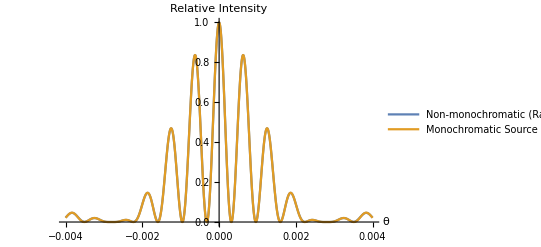

```mathematica
Plot[{adding[θ,5],double[θ,0.5,466*10^-9]},{θ,-0.004,0.004},PlotLegends->{"Non-monochromatic (Range = 10nm)","Monochromatic Source"},AxesLabel->{"θ","Relative Intensity"}]
```

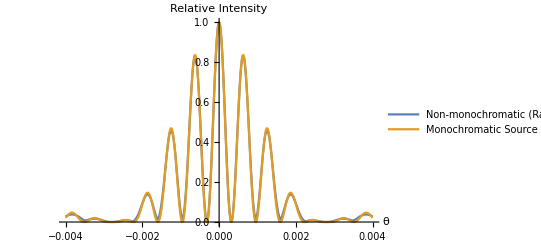

```mathematica
Plot[{adding[θ,20],double[θ,0.5,466*10^-9]},{θ,-0.004,0.004},PlotLegends->{"Non-monochromatic (Range = 40nm)","Monochromatic Source"},AxesLabel->{"θ","Relative Intensity"}]
```

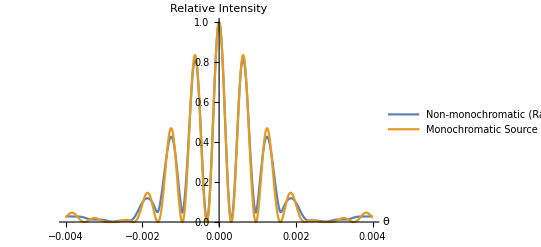

```mathematica
Plot[{adding[θ,40],double[θ,0.5,466*10^-9]},{θ,-0.004,0.004},PlotLegends->{"Non-monochromatic (Range = 80nm)","Monochromatic Source"},AxesLabel->{"θ","Relative Intensity"}]
```